```mathematica
SetDirectory[NotebookDirectory[]];
data = Import["DTM_ver2.dat", "Table"];
{h, w} = Dimensions[data]
```

{59,109}

```mathematica
Length[data[[1]]]
```

```mathematica
w
```

59

```mathematica
Reverse[{59,109}]
```

{109,59}

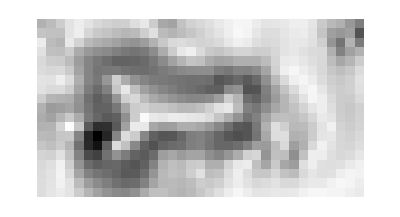

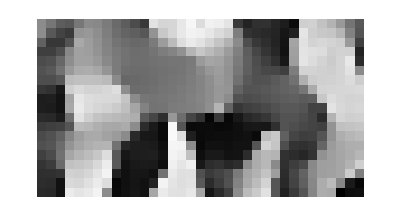

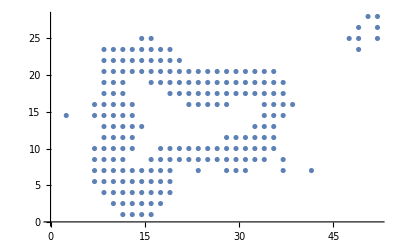

[(50.5, 28., 3.43419), (52., 28., 4.11491), (49., 26.5, 1.83145), (52., 26.5, 4.20269), (14.5, 25., 3.60986), (16., 25., 3.7164), (47.5, 25., 1.07282), (49., 25., 1.20541), (52., 25., 4.71968), (8.5, 23.5, 2.38619), (10., 23.5, 2.65774), (11.5, 23.5, 3.01852), (13., 23.5, 3.3065), (14.5, 23.5, 3.47021), (16., 23.5, 3.58811), (17.5, 23.5, 3.56313), (19., 23.5, 3.42934), (49., 23.5, 1.10239), (8.5, 22., 2.30613), (10., 22., 2.50762), (11.5, 22., 2.89676), (13., 22., 3.24401), (14.5, 22., 3.467), (16., 22., 3.56582), (17.5, 22., 3.57726), (19., 22., 3.49685), (20.5, 22., 3.44391), (8.5, 20.5, 2.02586), (10., 20.5, 2.17514), (11.5, 20.5, 2.60532), (13., 20.5, 3.2588), (14.5, 20.5, 3.56093), (16., 20.5, 3.62784), (17.5, 20.5, 3.61661), (19., 20.5, 3.55391), (20.5, 20.5, 3.49589), (22., 20.5, 3.44752), (23.5, 20.5, 3.39158), (25., 20.5, 3.24541), (26.5, 20.5, 2.91775), (28., 20.5, 2.55858), (29.5, 20.5, 2.42189), (31., 20.5, 2.70994), (32.5, 20.5, 3.33962), (34., 20.5, 3.93757), (35.5, 20.5, 4.31716), (8.5, 19., 1.54512), (10., 19., 1.57818), (11.5, 19., 1.70237), (16., 19., 3.70504), (17.5, 19., 3.63755), (19., 19., 3.56506), (20.5, 19., 3.48513), (22., 19., 3.41073), (23.5, 19., 3.34262), (25., 19., 3.21536), (26.5, 19., 3.03998), (28., 19., 2.78901), (29.5, 19., 2.486), (31., 19., 2.68861), (32.5, 19., 3.48749), (34., 19., 4.08818), (35.5, 19., 4.29353), (37., 19., 4.25066), (8.5, 17.5, 1.08744), (10., 17.5, 1.09585), (11.5, 17.5, 0.983039), (19., 17.5, 3.52136), (20.5, 17.5, 3.43094), (22., 17.5, 3.36796), (23.5, 17.5, 3.28914), (25., 17.5, 3.18022), (26.5, 17.5, 3.03466), (28., 17.5, 2.81304), (29.5, 17.5, 2.56444), (31., 17.5, 2.626), (32.5, 17.5, 3.84914), (34., 17.5, 4.24424), (35.5, 17.5, 4.22502), (37., 17.5, 4.10828), (7., 16., 0.611093), (8.5, 16., 0.835935), (10., 16., 0.921917), (11.5, 16., 0.9295), (13., 16., 0.983408), (22., 16., 3.31129), (23.5, 16., 3.24938), (25., 16., 3.1416), (26.5, 16., 3.01069), (28., 16., 2.79671), (34., 16., 4.41631), (35.5, 16., 4.32828), (37., 16., 4.21049), (38.5, 16., 4.0845), (2.5, 14.5, 5.59127), (7., 14.5, 0.54299), (8.5, 14.5, 0.853064), (10., 14.5, 1.01306), (11.5, 14.5, 1.10564), (13., 14.5, 1.29244), (34., 14.5, 4.74227), (35.5, 14.5, 4.63786), (37., 14.5, 4.48736), (8.5, 13., 1.18301), (10., 13., 1.46768), (11.5, 13., 1.62199), (13., 13., 1.72335), (14.5, 13., 1.8304), (32.5, 13., 5.69934), (34., 13., 5.30884), (35.5, 13., 5.16044), (8.5, 11.5, 1.75828), (10., 11.5, 1.97016), (11.5, 11.5, 2.15479), (13., 11.5, 2.17445), (28., 11.5, 6.01306), (29.5, 11.5, 6.05119), (31., 11.5, 6.02604), (32.5, 11.5, 5.90563), (34., 11.5, 5.72182), (35.5, 11.5, 5.7012), (7., 10., 2.38364), (8.5, 10., 2.12822), (10., 10., 2.10181), (11.5, 10., 2.28717), (13., 10., 2.46769), (17.5, 10., 5.69379), (19., 10., 5.71728), (20.5, 10., 6.06605), (22., 10., 0.146587), (23.5, 10., 0.816277), (25., 10., 5.50921), (26.5, 10., 6.04743), (28., 10., 5.97864), (29.5, 10., 5.96644), (31., 10., 5.96379), (32.5, 10., 5.90219), (34., 10., 5.87161), (35.5, 10., 6.03951), (7., 8.5, 2.20707), (8.5, 8.5, 1.99167), (10., 8.5, 1.87065), (11.5, 8.5, 1.84782), (16., 8.5, 5.5458), (17.5, 8.5, 5.56812), (19., 8.5, 5.6077), (20.5, 8.5, 5.91692), (22., 8.5, 0.248449), (23.5, 8.5, 0.271847), (25., 8.5, 2.835), (26.5, 8.5, 6.05042), (28., 8.5, 5.8761), (29.5, 8.5, 5.87318), (31., 8.5, 5.90844), (32.5, 8.5, 5.84956), (34., 8.5, 5.83373), (37., 8.5, 1.04964), (7., 7., 1.83921), (8.5, 7., 1.64374), (10., 7., 1.39165), (11.5, 7., 0.837934), (13., 7., 4.10695), (14.5, 7., 5.71149), (16., 7., 5.576), (17.5, 7., 5.54293), (19., 7., 5.5223), (23.5, 7., 0.416033), (28., 7., 5.66024), (29.5, 7., 5.66295), (31., 7., 5.83192), (37., 7., 1.73829), (41.5, 7., 5.19258), (7., 5.5, 1.4364), (8.5, 5.5, 1.28012), (10., 5.5, 0.966123), (11.5, 5.5, 0.469057), (13., 5.5, 4.1191), (14.5, 5.5, 5.8424), (16., 5.5, 5.67696), (17.5, 5.5, 5.61692), (19., 5.5, 5.65268), (8.5, 4., 1.00974), (10., 4., 0.69136), (11.5, 4., 0.287478), (13., 4., 5.48276), (14.5, 4., 5.88673), (16., 4., 5.74935), (17.5, 4., 5.75097), (19., 4., 5.88391), (10., 2.5, 0.490164), (11.5, 2.5, 0.845228), (13., 2.5, 6.11741), (14.5, 2.5, 5.88972), (16., 2.5, 5.77737), (17.5, 2.5, 5.85318), (11.5, 1., 2.82263), (13., 1., 6.05185), (14.5, 1., 5.85358), (16., 1., 5.74835), ]

```mathematica
gradx=Table[data[[y, x+1]]-data[[y, x-1]](*,data[[y+1, x]]-data[[y-1, x]]}*),{y,2, h-1},{x,2,w-1}];
grady=Table[data[[y+1, x]]-data[[y-1, x]],{y,2, h-1},{x,2,w-1}];
gradabs =ArcTan[√(gradx gradx + grady grady)];
rot=ArcTan[ grady,-gradx+0.000001]+Pi;
flat=Map[Mean,Partition[gradabs,3]];
mini = Transpose[Map[Mean,Partition[Transpose[flat],3]]];
flatr=Map[Mean,Partition[rot,3]];
minir= Transpose[Map[Mean,Partition[Transpose[flatr],3]]];
xs = Range[1,(w-1)/2,1.5];
ys = Range[(h-1)/2,1,-1.5];
positions = Table[{x,y},{y,ys},{x,xs}];
ArrayPlot[mini]
ArrayPlot[minir]
allpoints = Flatten[Table[{xs[[x]],ys[[y]],mini[[y,x]], minir[[y,x]]},{y,Length[ys]},{x,Length[xs]}],1];
slopepoints = Select[allpoints, #[[3]] > 10/180*Pi&];
ListPlot[Map[#[[1;;2]]&,slopepoints]]
"["<>StringJoin[Table["("<>ToString[p[[1]]]<>", "<>ToString[p[[2]]]<>", "<>ToString[p[[4]]]<>"), ",{p, slopepoints}]]<>"]"
```

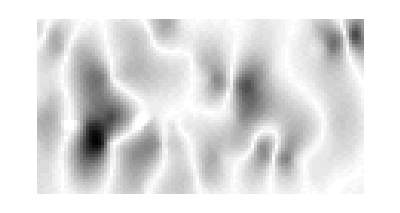

```mathematica
ArrayPlot[gradx]
```